# ChebyshevPsi

Calculate the value of the second Chebyshev function ψ(x).

## DefinitionDefinitionDefine your function using the name above. All definitions, including dependencies, will be included in the resource function when it is generated. Additional cells can be added and definitions can be given for multiple input cases. This section should be evaluated before evaluating creating the Examples section below.

```mathematica
ChebyshevPsi[x_]:=Sum[MangoldtLambda[n],{n,2,Floor[x]}]
```

## Documentation

### UsageUsageDocument every accepted input usage case. Use Enter to create new cases as needed. Each usage should contain a brief explanation saying what the function does for the given input structure. See existing documentation pages for examples.

ChebyshevPsi[x]

returns the value of the second Chebyshev function at x.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used. Add multiple cells including tables and hyperlinks as needed. Typical information includes: acceptable inputs, result formats, options specifications, and background information.

The second Chebysev function ψ(x) is calulated by summing the Mangoldt function from 2 to the greatest integer less than or equal to x. If x<2 the defining sum is empty and by convention we set ψ(x)=0.

The Prime Number Theorem is equivalent to the statement that (ψ(x))/x→1 as x→∞

## ExamplesExamplesDemonstrate how to use the function. Examples should start with the most basic use case. Each example should be described using text cells. Use "Subsection" and "Subsubsection" cells to group examples as needed. See existing documentation pages for examples.

### Basic Examples

Compute ψ(30):

```mathematica
ChebyshevPsi[30]
```

4 Log[2]+3 Log[3]+2 Log[5]+Log[7]+Log[11]+Log[13]+Log[17]+Log[19]+Log[23]+Log[29]

Obtain a decimal approximation:

```mathematica
ChebyshevPsi[30]//N
```

28.4765

Plot ψ(x) from 0 to 30:

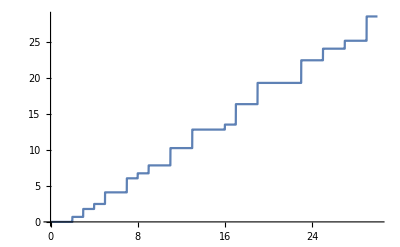

```mathematica
Plot[ChebyshevPsi[x],{x,0,30}]
```

Compare x, ψ(x), and |x-ψ(x)|:

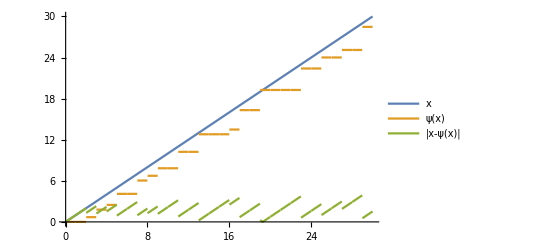

```mathematica
Plot[{x,ChebyshevPsi[x],Abs[x-ChebyshevPsi[x]]},{x,0,30},PlotLegends->{"x","ψ(x)","|x-ψ(x)|"}]
```

Plot the ratio (ψ(x))/x:

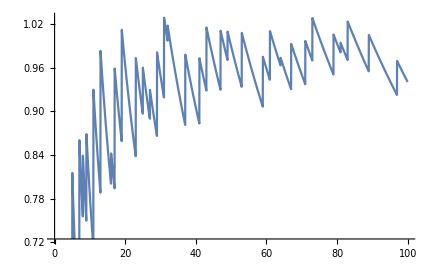

```mathematica
Plot[ChebyshevPsi[x]/x,{x,0,100}]
```

## Source & Additional Information

### Contributed ByContributed ByName of the person, people or organization that should be publicly credited with contributing the function.

Jack Heimrath

### KeywordsKeywordsList relevant terms that should be used to include this resource in search results.

Analytic Number Theory

Prime Number Theorem

Prime Numbers

### Related SymbolsRelated SymbolsList related Wolfram Language symbols. Include up to twenty documented, system-level symbols.

MangoldtLambda

Log

### Related Resource ObjectsRelated Resource ObjectsNames of published resource objects from any Wolfram repository that are related to this resource.

Resource Name (resources from any Wolfram repository)

### Source/Reference CitationSource/Reference CitationCitation for original source of the function or its components. For example, original publication of an algorithm or public code repository.

### LinksLinksURLs or hyperlinks for external information related to the function.

### TestsTestsOptional list of tests that can be used to verify that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as literal VerificationTest expressions if you need to specify options.

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.